# Autovalores de una caminata discreta en un rectangulo de 10 x 5

Ejecuta las celdas de arriba hacia abajo. El kernel principal esta en tu Mac; el calculo se envia por SSH a Mazinger y luego a nodo1. No se guardan archivos en el cluster.

## Modelo de un paso

GenerateRectangleBasis[9, 4] produce 10 x 5 = 50 posiciones. Cada posicion tiene cuatro estados de moneda: arriba, abajo, derecha e izquierda. BuildShiftOperators[base, CoinDimension -> 4] construye S con reflexion en la frontera. La moneda de Grover C = GeneralizedGroverCoin[Pi/4] se aplica en cada posicion. El operador de un paso es U = S . (I_50 KroneckerProduct C) y mide 200 x 200.

## Construccion y diagonalizacion en nodo1

PacletDirectoryLoad hace visible QuantumWalks solo durante esta sesion temporal del nodo. Needs carga todo el paquete. ForScience ya esta instalado en tu cuenta; Block usa texto simple para las ayudas durante la carga porque este kernel no tiene interfaz grafica. No cambia los calculos.

```mathematica
resultadoDiscreto = RemoteEvaluate["ssh://robot", RemoteEvaluate["ssh://nodo1", Module[{ruta, base, s, moneda, monedaGlobal, u, vals, dim}, ruta = "/home/saul/QW/JA_libs/QuantumWalks"; PacletDirectoryLoad[ruta]; Needs["ForScience`"]; Block[{ForScience`PacletUtils`FormatUsage = Identity}, Needs["QuantumWalks`"]]; base = QuantumWalks`Billiards`GenerateRectangleBasis[9, 4]; dim = base["Dimension"]; s = QuantumWalks`Billiards`BuildShiftOperators[base, QuantumWalks`Billiards`CoinDimension -> 4]; moneda = QuantumWalks`Billiards`GeneralizedGroverCoin[Pi/4.]; monedaGlobal = KroneckerProduct[IdentityMatrix[dim, SparseArray], SparseArray[moneda]]; u = s . monedaGlobal; vals = Eigenvalues[Normal[u]]; <|"Nodo" -> $MachineName, "Sitios" -> dim, "DimensionU" -> Dimensions[u], "Autovalores" -> vals, "ErrorUnitariedad" -> Max[Abs[Flatten[ConjugateTranspose[u] . u - IdentityMatrix[4 dim]]]], "ErrorModulo" -> Max[Abs[Abs[vals] - 1]]|>]]]
```

<|Nodo→nodo1,Sitios→50,DimensionU→{200,200},Autovalores→{1.+0. ⅈ,0.154508+0.987991 ⅈ,0.154508-0.987991 ⅈ,-0.309017+0.951057 ⅈ,-0.309017-0.951057 ⅈ,-0.110616+0.993863 ⅈ,-0.110616-0.993863 ⅈ,-0.904508+0.426456 ⅈ,-0.904508-0.426456 ⅈ,-0.630037+0.776565 ⅈ,-0.630037-0.776565 ⅈ,-0.345492+0.938422 ⅈ,-0.345492-0.938422 ⅈ,1.+0. ⅈ,-1.+0. ⅈ,1.+0. ⅈ,-0.0954915+0.99543 ⅈ,-0.0954915-0.99543 ⅈ,1.+0. ⅈ,-0.25+0.968246 ⅈ,-0.25-0.968246 ⅈ,-0.0244717+0.999701 ⅈ,-0.0244717-0.999701 ⅈ,-0.698401+0.715707 ⅈ,-0.698401-0.715707 ⅈ,-1.+0. ⅈ,-0.5+0.866025 ⅈ,-0.5-0.866025 ⅈ,1.+0. ⅈ,0.0710198+0.997475 ⅈ,0.0710198-0.997475 ⅈ,-1.+0. ⅈ,-0.809017+0.587785 ⅈ,-0.809017-0.587785 ⅈ,0.559017+0.829156 ⅈ,0.559017-0.829156 ⅈ,0.880037+0.474906 ⅈ,0.880037-0.474906 ⅈ,-0.654508+0.756055 ⅈ,-0.654508-0.756055 ⅈ,-0.404508+0.914534 ⅈ,-0.404508-0.914534 ⅈ,-0.345492+0.938422 ⅈ,-0.345492-0.938422 ⅈ,1.66533×10^-16+1. ⅈ,1.66533×10^-16-1. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.32102+0.947072 ⅈ,0.32102-0.947072 ⅈ,-1.+0. ⅈ,2.15106×10^-16+1. ⅈ,2.15106×10^-16-1. ⅈ,-0.880037+0.474906 ⅈ,-0.880037-0.474906 ⅈ,0.809017+0.587785 ⅈ,0.809017-0.587785 ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+3.14018×10^-16 ⅈ,-1.-3.14018×10^-16 ⅈ,0.309017+0.951057 ⅈ,0.309017-0.951057 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,0.139384+0.990238 ⅈ,0.139384-0.990238 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-0.32102+0.947072 ⅈ,-0.32102-0.947072 ⅈ,0.25+0.968246 ⅈ,0.25-0.968246 ⅈ,1.+4.6444×10^-16 ⅈ,1.-4.6444×10^-16 ⅈ,1.+3.04047×10^-16 ⅈ,1.-3.04047×10^-16 ⅈ,1.+2.4037×10^-16 ⅈ,1.-2.4037×10^-16 ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-0.793893+0.608058 ⅈ,-0.793893-0.608058 ⅈ,0.+1. ⅈ,0.-1. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-0.154508+0.987991 ⅈ,-0.154508-0.987991 ⅈ,-1.+0. ⅈ,-1.+2.48253×10^-16 ⅈ,-1.-2.48253×10^-16 ⅈ,1.+5.43896×10^-16 ⅈ,1.-5.43896×10^-16 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,1.+2.35514×10^-16 ⅈ,1.-2.35514×10^-16 ⅈ,1.+2.35514×10^-16 ⅈ,1.-2.35514×10^-16 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-0.904508+0.426456 ⅈ,-0.904508-0.426456 ⅈ,1.+1.8619×10^-16 ⅈ,1.-1.8619×10^-16 ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,1.+0. ⅈ,-0.559017+0.829156 ⅈ,-0.559017-0.829156 ⅈ,-0.448401+0.893832 ⅈ,-0.448401-0.893832 ⅈ,-0.206107+0.978529 ⅈ,-0.206107-0.978529 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+2.71948×10^-16 ⅈ,-1.-2.71948×10^-16 ⅈ,-1.11022×10^-16+1. ⅈ,-1.11022×10^-16-1. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-0.559017+0.829156 ⅈ,-0.559017-0.829156 ⅈ,-0.25+0.968246 ⅈ,-0.25-0.968246 ⅈ,0.404508+0.914534 ⅈ,0.404508-0.914534 ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-0.0710198+0.997475 ⅈ,-0.0710198-0.997475 ⅈ,0.630037+0.776565 ⅈ,0.630037-0.776565 ⅈ,0.698401+0.715707 ⅈ,0.698401-0.715707 ⅈ,1.+0. ⅈ,-1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.110616+0.993863 ⅈ,0.110616-0.993863 ⅈ,1.+0. ⅈ,0.25+0.968246 ⅈ,0.25-0.968246 ⅈ,1.+0. ⅈ,-1.+0. ⅈ,1.+0. ⅈ,0.448401+0.893832 ⅈ,0.448401-0.893832 ⅈ,1.+0. ⅈ,-0.139384+0.990238 ⅈ,-0.139384-0.990238 ⅈ,0.559017+0.829156 ⅈ,0.559017-0.829156 ⅈ,-0.975528+0.219874 ⅈ,-0.975528-0.219874 ⅈ,-0.0954915+0.99543 ⅈ,-0.0954915-0.99543 ⅈ,-0.654508+0.756055 ⅈ,-0.654508-0.756055 ⅈ},ErrorUnitariedad→2.22045×10^-16,ErrorModulo→5.32907×10^-15|>

## Comprobaciones

```mathematica
{resultadoDiscreto["Nodo"], resultadoDiscreto["Sitios"], resultadoDiscreto["DimensionU"], Length[resultadoDiscreto["Autovalores"]], resultadoDiscreto["ErrorUnitariedad"], resultadoDiscreto["ErrorModulo"]}
```

{nodo1,50,{200,200},200,2.22045×10^-16,5.32907×10^-15}

Resultado esperado: {"nodo1", 50, {200, 200}, 200, errores cercanos a 10^-15}. Los errores pequenos reflejan el redondeo numerico.

## Autovalores complejos

```mathematica
resultadoDiscreto["Autovalores"]
```

{1.+0. ⅈ,0.154508+0.987991 ⅈ,0.154508-0.987991 ⅈ,-0.309017+0.951057 ⅈ,-0.309017-0.951057 ⅈ,-0.110616+0.993863 ⅈ,-0.110616-0.993863 ⅈ,-0.904508+0.426456 ⅈ,-0.904508-0.426456 ⅈ,-0.630037+0.776565 ⅈ,-0.630037-0.776565 ⅈ,-0.345492+0.938422 ⅈ,-0.345492-0.938422 ⅈ,1.+0. ⅈ,-1.+0. ⅈ,1.+0. ⅈ,-0.0954915+0.99543 ⅈ,-0.0954915-0.99543 ⅈ,1.+0. ⅈ,-0.25+0.968246 ⅈ,-0.25-0.968246 ⅈ,-0.0244717+0.999701 ⅈ,-0.0244717-0.999701 ⅈ,-0.698401+0.715707 ⅈ,-0.698401-0.715707 ⅈ,-1.+0. ⅈ,-0.5+0.866025 ⅈ,-0.5-0.866025 ⅈ,1.+0. ⅈ,0.0710198+0.997475 ⅈ,0.0710198-0.997475 ⅈ,-1.+0. ⅈ,-0.809017+0.587785 ⅈ,-0.809017-0.587785 ⅈ,0.559017+0.829156 ⅈ,0.559017-0.829156 ⅈ,0.880037+0.474906 ⅈ,0.880037-0.474906 ⅈ,-0.654508+0.756055 ⅈ,-0.654508-0.756055 ⅈ,-0.404508+0.914534 ⅈ,-0.404508-0.914534 ⅈ,-0.345492+0.938422 ⅈ,-0.345492-0.938422 ⅈ,1.66533×10^-16+1. ⅈ,1.66533×10^-16-1. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.32102+0.947072 ⅈ,0.32102-0.947072 ⅈ,-1.+0. ⅈ,2.15106×10^-16+1. ⅈ,2.15106×10^-16-1. ⅈ,-0.880037+0.474906 ⅈ,-0.880037-0.474906 ⅈ,0.809017+0.587785 ⅈ,0.809017-0.587785 ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+3.14018×10^-16 ⅈ,-1.-3.14018×10^-16 ⅈ,0.309017+0.951057 ⅈ,0.309017-0.951057 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,0.139384+0.990238 ⅈ,0.139384-0.990238 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-0.32102+0.947072 ⅈ,-0.32102-0.947072 ⅈ,0.25+0.968246 ⅈ,0.25-0.968246 ⅈ,1.+4.6444×10^-16 ⅈ,1.-4.6444×10^-16 ⅈ,1.+3.04047×10^-16 ⅈ,1.-3.04047×10^-16 ⅈ,1.+2.4037×10^-16 ⅈ,1.-2.4037×10^-16 ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-0.793893+0.608058 ⅈ,-0.793893-0.608058 ⅈ,0.+1. ⅈ,0.-1. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-0.154508+0.987991 ⅈ,-0.154508-0.987991 ⅈ,-1.+0. ⅈ,-1.+2.48253×10^-16 ⅈ,-1.-2.48253×10^-16 ⅈ,1.+5.43896×10^-16 ⅈ,1.-5.43896×10^-16 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,1.+2.35514×10^-16 ⅈ,1.-2.35514×10^-16 ⅈ,1.+2.35514×10^-16 ⅈ,1.-2.35514×10^-16 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-0.904508+0.426456 ⅈ,-0.904508-0.426456 ⅈ,1.+1.8619×10^-16 ⅈ,1.-1.8619×10^-16 ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,1.+0. ⅈ,-0.559017+0.829156 ⅈ,-0.559017-0.829156 ⅈ,-0.448401+0.893832 ⅈ,-0.448401-0.893832 ⅈ,-0.206107+0.978529 ⅈ,-0.206107-0.978529 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+2.71948×10^-16 ⅈ,-1.-2.71948×10^-16 ⅈ,-1.11022×10^-16+1. ⅈ,-1.11022×10^-16-1. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-0.559017+0.829156 ⅈ,-0.559017-0.829156 ⅈ,-0.25+0.968246 ⅈ,-0.25-0.968246 ⅈ,0.404508+0.914534 ⅈ,0.404508-0.914534 ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-0.0710198+0.997475 ⅈ,-0.0710198-0.997475 ⅈ,0.630037+0.776565 ⅈ,0.630037-0.776565 ⅈ,0.698401+0.715707 ⅈ,0.698401-0.715707 ⅈ,1.+0. ⅈ,-1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.110616+0.993863 ⅈ,0.110616-0.993863 ⅈ,1.+0. ⅈ,0.25+0.968246 ⅈ,0.25-0.968246 ⅈ,1.+0. ⅈ,-1.+0. ⅈ,1.+0. ⅈ,0.448401+0.893832 ⅈ,0.448401-0.893832 ⅈ,1.+0. ⅈ,-0.139384+0.990238 ⅈ,-0.139384-0.990238 ⅈ,0.559017+0.829156 ⅈ,0.559017-0.829156 ⅈ,-0.975528+0.219874 ⅈ,-0.975528-0.219874 ⅈ,-0.0954915+0.99543 ⅈ,-0.0954915-0.99543 ⅈ,-0.654508+0.756055 ⅈ,-0.654508-0.756055 ⅈ}

Los autovalores de un operador unitario deben estar sobre el circulo unitario. Algunos pueden coincidir y verse como un solo punto.

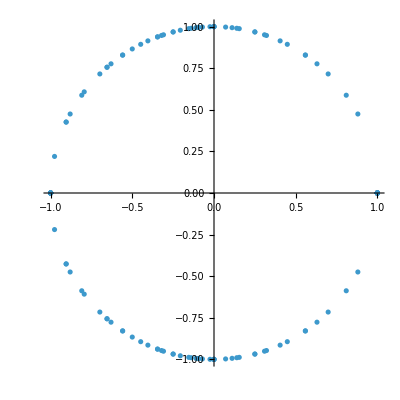

```mathematica
ComplexListPlot[resultadoDiscreto["Autovalores"], PlotRange -> All, AspectRatio -> 1]
```

## Fases y cuasienergias

Si lambda_j = Exp[-I epsilon_j], entonces epsilon_j = -Arg[lambda_j] modulo 2 Pi. Elegimos la rama entre 0 y 2 Pi.

```mathematica
cuasienergias = Sort[Mod[-Arg[resultadoDiscreto["Autovalores"]], 2 Pi]]
```

```mathematica
ListPlot[cuasienergias, Frame -> True, FrameLabel -> {"indice ordenado", "cuasienergia"}, PlotRange -> All]
```